```mathematica
ClearAll["Global`*"]
$Assumptions={s>0, σ>0};
```

Using classical time-dependent perturbation theory gives the first order transfer matrix as

```mathematica
M11[s_]=1-I0[s] s+I1[s];
M12[s_]=s-I1[s] s+I2[s];
M21[s_]=-I0[s];
M22[s_]=1-I1[s];
β[s_]=M11[s]^2 β0-2 M11[s] M12[s] α0+M12[s]^2 γ0
```

β0 (1-s I0[s]+I1[s])^2-2 α0 (1-s I0[s]+I1[s]) (s-s I1[s]+I2[s])+γ0 (s-s I1[s]+I2[s])^2

```mathematica
Expand[%]
```

-2 s α0+β0+s^2 γ0+2 s^2 α0 I0[s]-2 s β0 I0[s]+s^2 β0 I0[s]^2+2 β0 I1[s]-2 s^2 γ0 I1[s]-2 s^2 α0 I0[s] I1[s]-2 s β0 I0[s] I1[s]+2 s α0 I1[s]^2+β0 I1[s]^2+s^2 γ0 I1[s]^2-2 α0 I2[s]+2 s γ0 I2[s]+2 s α0 I0[s] I2[s]-2 α0 I1[s] I2[s]-2 s γ0 I1[s] I2[s]+γ0 I2[s]^2

For some reason this doesn’t work well for the beta function, lets check each step one at a time.

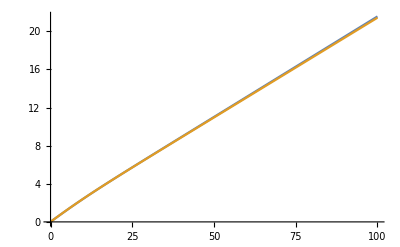

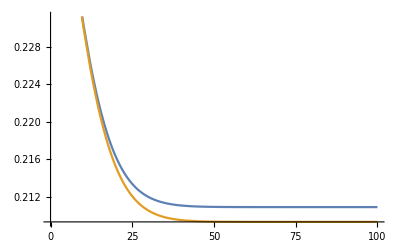

```mathematica
η[s_]=Piecewise[{{0.05,s<1},{0,s≥1}}];
η[s_]=Exp[-(s+80)^2/(2 24^2)];
sf=100;
y0=.01;
yp0=.25;
I0[s_]=∫_0^s η[x] ⅆx;
I1[s_]=∫_0^s x η[x] ⅆx;
I2[s_]=∫_0^s x^2 η[x] ⅆx;
sol=NDSolve[{y''[s]==-η[s] y[s],y[0]==y0,y'[0]==yp0},y,{s,0,sf}];
ya[s_]=y0 (1-I0[s] s+I1[s])+yp0 ((1-I1[s]) s+I2[s]);
ypa[s_]=-y0 I0[s]+yp0 (1-I1[s]);
Plot[{Evaluate[y[s]/.sol],ya[s]},{s,0,sf}]
Plot[{Evaluate[y'[s]/.sol],ypa[s]},{s,0,sf}]
```

Lets use classical time dependent perturbation theory to try and find how the beam evolves. We get two integrals for the new coordinates which can be solved for certain plasma density profiles.

```mathematica
η[s_]=Exp[(s-s0)^2/(2 σr^2)];
A1[s_]=-∫_0^s (yp0 sp+y0) η[sp] ⅆsp
B1[s_]=∫_0^s sp (yp0 sp+y0) η[sp] ⅆsp
```

-1/2 σr (2 (ⅇ^((s-s0)^2/(2 σr^2))-ⅇ^(s0^2/(2 σr^2))) yp0 σr+√(2 π) (y0+s0 yp0) (Erfi[(s-s0)/(√2 σr)]+Erfi[s0/(√2 σr)]))

ⅇ^((s0 (-2 s+s0))/(2 σr^2)) (-ⅇ^((s s0)/σr^2) (y0+s0 yp0)+ⅇ^(s^2/(2 σr^2)) (y0+(s+s0) yp0)) σr^2+√(π/2) σr (s0 (y0+s0 yp0)-yp0 σr^2) (Erfi[(s-s0)/(√2 σr)]+Erfi[s0/(√2 σr)])

For a very short Gaussian ramp we can calculate the asymptotic vacuum waist exactly.

```mathematica
η[s_]=Exp[-s^2/(2 σ^2)];
I0=∫_0^∞ η[x] ⅆx
I1=∫_0^∞ x η[x] ⅆx
I2=∫_0^∞ x^2 η[x] ⅆx
```

√(π/2) σ

σ^2

√(π/2) σ^3